https://journals.aps.org/pr/abstract/10.1103/PhysRev.155.1404

## Equation 12: L’[w0] as series

π^2/12+PolyLog[2,-1/w0]

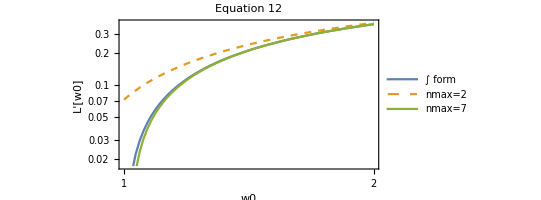

```mathematica
Clear[Lpint,Lpser]
π^2/12-Sum[(-1)^(n-1)/(n^2 w0^n),{n,1,∞}]
Lpint[w0_]:=NIntegrate[1/w Log[1+1/w],{w,1,w0}]
Lpser[w0_,nmax_]:=π^2/12-Sum[(-1)^(n-1)/(n^2 w0^n),{n,1,nmax}]
LogLogPlot[{Lpint[w0],Lpser[w0,2],Lpser[w0,7]},{w0,1,2},PlotPoints->2,PlotStyle->{Default,Dashed},AspectRatio->0.5,Frame->True,FrameLabel->{"w0","L'[w0]"},PlotLegends->{"∫ form","nmax=2","nmax=7"},PlotLabel->"Equation 12"]
```

## Figure 1

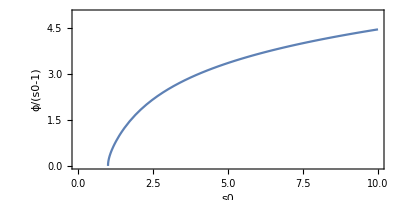

```mathematica
Clear[σ,β,r0,ϕ9,s0]

(* equation 4 defines β as function of s *)
(1-β^2)((3-β^4)Log[(1+β)/(1-β)]-2β(2-β^2))/.{β->Sqrt[1-1/s]};

(* total cross section *)
σ[s_]:=(-2 √(1-1/s) (1+1/s)+(3-(1-1/s)^2) Log[(1+√(1-1/s))/(1-√(1-1/s))])/s(* multiplied by (π r0^2)/2*)

(* function to plot in figure 1 *)
ϕ9[s0_]:=NIntegrate[s σ[s],{s,1,s0}](* divided by 2/(π r0^2)*)
Plot[ϕ9[s0]/(s0-1),{s0,1,10},PlotRange->{{0,10},{0,5}},AspectRatio->0.5,Frame->True,FrameLabel->{"s0","ϕ/(s0-1)"}]
```

## Equation 13: asymptotic formulas

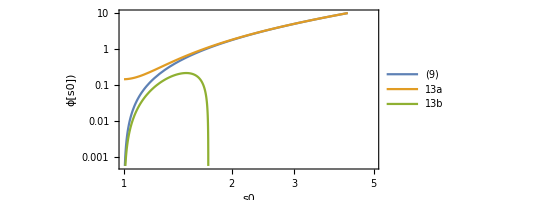

```mathematica
Clear[σ,β,r0,ϕ9,s0,ϕ13a,ϕ13b]
ϕ9[s0_]:=NIntegrate[s (-2 √(1-1/s) (1+1/s)+(3-(1-1/s)^2) Log[(1+√(1-1/s))/(1-√(1-1/s))])/s,{s,1,s0}]
ϕ13a[s0_]:=2s0(Log[4s0]-2)+Log[4s0](Log[4s0]-2)-(π^2-9)/3+1/s0(Log[4s0]+9/8)
ϕ13b[s0_]:=2/3(s0-1)^1.5+5/3(s0-1)^2.5-1507/420(s0-1)^3.5
LogLogPlot[{ϕ9[s0],ϕ13a[s0],ϕ13b[s0]},{s0,1,5},PlotRange->{{0,5},{0,10}},AspectRatio->0.5,Frame->True,FrameLabel->{"s0","ϕ[s0])"},PlotLegends->{"(9)","13a","13b"}]
```

## Figure 2: graph of function eq. (18)

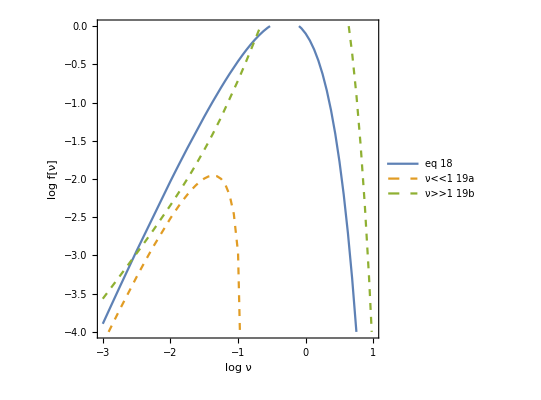

```mathematica
Clear[ν,f]
Clear[σ,β,r0,ϕ9,s0,Fβ,σm,s]
ϕ9[s0_?NumericQ]:=ϕ9[s0]=NIntegrate[s (-2 √(1-1/s) (1+1/s)+(3-(1-1/s)^2) Log[(1+√(1-1/s))/(1-√(1-1/s))])/s,{s,1,s0}]
f[ν_?NumericQ]:=f[ν]=ν^2 NIntegrate[(Exp[ϵ]-1)^(-1) ϕ9[ϵ/ν],{ϵ,ν,∞}]

Plot[{Log[f[10^logν]],Log[(π^2/3)10^logν Log[0.117/10^logν]],Log[((π 10^logν)/4)^0.5 Exp[-(10^logν)] (1+75/8 10^logν)]},{logν,-3,1},AspectRatio->1,Frame->True,FrameLabel->{"log ν","log f[ν]"},PlotPoints->2,PlotRange->{{-3,1},{-4,0}},PlotLegends->{"eq 18","ν<<1 19a","ν>>1 19b"},PlotStyle->{Default,Dashed,Dashed}]
```

```mathematica
(* maximum value ~1 at ν ~1, but to be more precise *)
FindMaximum[f[ν],{ν,0.5}]
```

{1.07603,{ν→0.503615}}

## Figure 3: graph of function eq. (23)

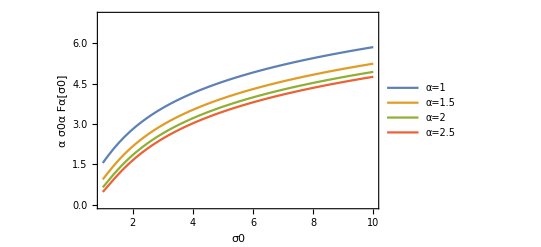

```mathematica
Clear[σ,β,r0,ϕ9,s0,Fα,σm,s,eqFig3]
ϕ9[s0_?NumericQ]:=ϕ9[s0]=NIntegrate[s (-2 √(1-1/s) (1+1/s)+(3-(1-1/s)^2) Log[(1+√(1-1/s))/(1-√(1-1/s))])/s,{s,1,s0}]
Fα[σ0_?NumericQ,α_?NumericQ]:=Fα[σ0,α]=NIntegrate[s0^(-α-2)ϕ9[s0],{s0,σ0,∞}]
eqFig3[σ0_?NumericQ,α_?NumericQ]:=eqFig3[σ0,α]=α σ0^α Fα[σ0,α]
Plot[{eqFig3[σ0,1],eqFig3[σ0,1.5],eqFig3[σ0,2],eqFig3[σ0,2.5]},{σ0,1,10},PlotRange->{{1,10},{0,7}},Frame->True,FrameLabel->{"σ0","α σ0α Fα[σ0]"},PlotLegends->{"α=1","α=1.5","α=2","α=2.5"}]
```

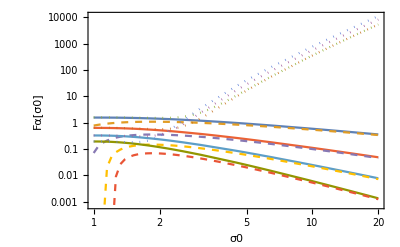

```mathematica
LogLogPlot[{Fα[σ0,1],(2/(α σ0^α)(Log[4σ0]+1/α-2))/.{α->1},(Fα1-4/15(σ0-1)^2.5+(2/21(2α-1))(σ0-1)^3.5)/.{Fα1->1.579,α->1.5},Fα[σ0,1.5],(2/(α σ0^α)(Log[4σ0]+1/α-2))/.{α->1.5},(Fα1-4/15(σ0-1)^2.5+(2/21(2α-1))(σ0-1)^3.5)/.{Fα1->0.6373,α->1.5},Fα[σ0,2],(2/(α σ0^α)(Log[4σ0]+1/α-2))/.{α->2},(Fα1-4/15(σ0-1)^2.5+(2/21(2α-1))(σ0-1)^3.5)/.{Fα1->0.3275,α->2},Fα[σ0,2.5],(2/(α σ0^α)(Log[4σ0]+1/α-2))/.{α->2.5},(Fα1-4/15(σ0-1)^2.5+(2/21(2α-1))(σ0-1)^3.5)/.{Fα1->0.1932,α->2.5}},{σ0,1,20},Frame->True,FrameLabel->{"σ0","Fα[σ0]"},PlotStyle->{Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted},PlotPoints->2]
```

## Figure 4: graph of function eq. (28)

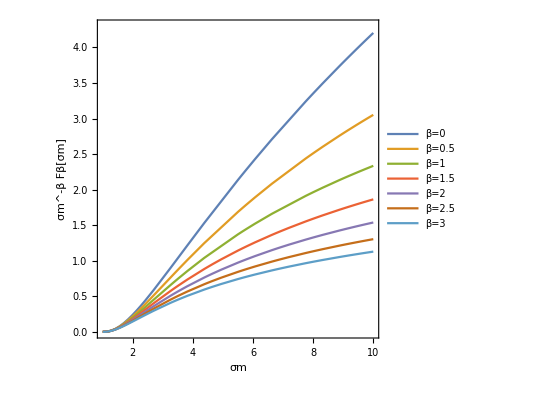

```mathematica
Clear[σ,β,r0,ϕ9,s0,Fβ,σm,s]
ϕ9[s0_?NumericQ]:=ϕ9[s0]=NIntegrate[s (-2 √(1-1/s) (1+1/s)+(3-(1-1/s)^2) Log[(1+√(1-1/s))/(1-√(1-1/s))])/s,{s,1,s0}]
Fβ[σm_?NumericQ,β_?NumericQ]:=Fβ[σm,β]=NIntegrate[s0^(β-2)ϕ9[s0],{s0,1,σm}]
eq28[σm_,β_]:=σm^(-β) Fβ[σm,β]
Plot[{eq28[σm,0],eq28[σm,0.5],eq28[σm,1],eq28[σm,1.5],eq28[σm,2],eq28[σm,2.5],eq28[σm,3]},{σm,1,10},PlotPoints->2,PlotRange->{{1,10},{0,4.3}},Frame->True,FrameLabel->{"σm","σm^-β Fβ[σm]"},PlotLegends->{"β=0","β=0.5","β=1","β=1.5","β=2","β=2.5","β=3"},AspectRatio->1]
```

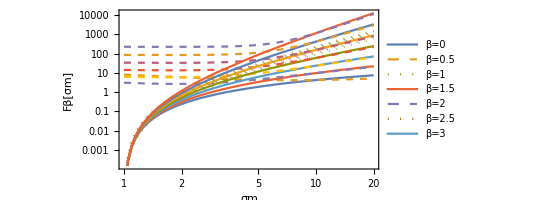

```mathematica
Clear[σ,β,r0,ϕ9,s0,Fβ,σm,s,A,eq29a,eq29b]
ϕ9[s0_?NumericQ]:=ϕ9[s0]=NIntegrate[s (-2 √(1-1/s) (1+1/s)+(3-(1-1/s)^2) Log[(1+√(1-1/s))/(1-√(1-1/s))])/s,{s,1,s0}]
Fβ[σm_?NumericQ,β_?NumericQ]:=Fβ[σm,β]=NIntegrate[s0^(β-2)ϕ9[s0],{s0,1,σm}]
eq28[σm_,β_]:=σm^(-β) Fβ[σm,β]
A[β_]:=Piecewise[{{8.111,β==0},{13.53,β==0.5},{9.489,β==1},{15.675,β==1.5},{34.54,β==2},{85.29,β==2.5},{222.9,β==3}}]
eq29a[σm_,β_]:=Piecewise[{{A[β]+Log[σm]^2-4Log[σm],β==0},{A[β]+2/β σm^β (Log[4σm]-1/β-2),β!=0}}]
eq29b[σm_,β_]:=4/15(σm-1)^2.5+(2/21(2β+1))(σm-1)^2.5
LogLogPlot[{Fβ[σm,0],eq29a[σm,0],eq29b[σm,0],Fβ[σm,0.5],eq29a[σm,0.5],eq29b[σm,0.5],Fβ[σm,1],eq29a[σm,1],eq29b[σm,1],Fβ[σm,1.5],eq29a[σm,1.5],eq29b[σm,1.5],Fβ[σm,2],eq29a[σm,2],eq29b[σm,2],Fβ[σm,2.5],eq29a[σm,2.5],eq29b[σm,2.5],Fβ[σm,3],eq29a[σm,3],eq29b[σm,3]},{σm,1,20},PlotPoints->2,Frame->True,FrameLabel->{"σm","Fβ[σm]"},PlotLegends->{"β=0","β=0.5","β=1","β=1.5","β=2","β=2.5","β=3"},AspectRatio->0.5,PlotStyle->{Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted,Default,Dashed,Dotted}]
```